# Mathematica 入门 之 可视化 2024-01-29 Bilibili @江湖人称剑客陈

## 概述

Mathematica 中可视化的种类

Mathematica 拥有强大易用的可视化功能，可以轻松绘制各类数据、函数、几何物体，更有针对向量场、统计数据、复变函数、地理信息等领域的专门绘图函数。

所有这些绘图都支持二维和三维，可以自由组合，定制标注、图例、坐标轴、色彩甚至光照效果。内置的自适应采样算法可以兼顾精度和效率，无需手动设置即可获得高质量图像。

除了缩放、旋转视角等基本交互，Mathematica 中的动态交互功能更为绘图增添了无限可能。通过滑块、按钮、定位器等丰富控件，可以实时调整参数，实现交互式演示。

Mathematica 中可视化的特点

函数式语法 —— 输入进函数，输出一个绘图。

语法简洁、高度统一，简单易用

动态交互性强

智能自适应算法：
在曲率大的地方多采样
符号式 → 智能 → 快速

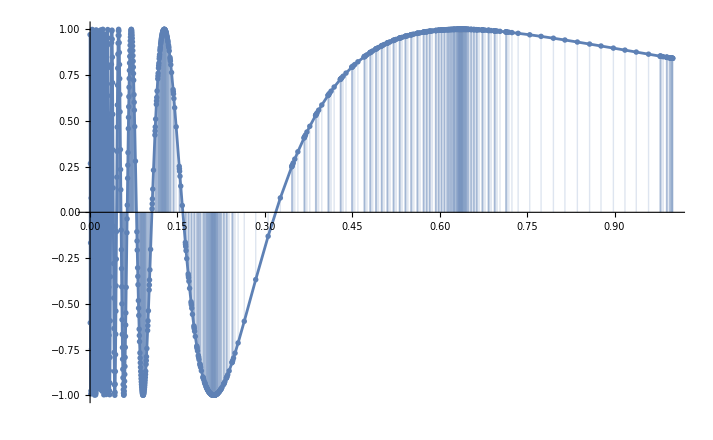

```mathematica
Plot[Sin[1/x],{x,0,1}];
First@Cases[%,Line[list_]:>ListPlot[list,Filling->Axis,FillingStyle->Opacity[.2]],All];
Show[%,%%]
```

相关帮助文档

帮助文档首页 - 可视化与图形

选中函数 / 文档路径，按 F1 键（可能需要加上 fn 功能键）即可查看对应帮助文档界面

## 绘图函数分类导览

帮助文档：
guide/FunctionVisualization 函数可视化
guide/DataVisualization 数据可视化

所有名字里带 Plot 或者 Chart 的函数（包括选项）

```mathematica
??*Plot*
```

```mathematica
??*Chart*
```

## 图形 Graphics & Graphics3D

前面我们讲了各种各样的绘图函数，基本上都是 *Plot* 或者 *Chart* 这样的格式，它们负责把「函数」和「数据」可视化出来。

另一类非常重要的可视化，是「画一个几何物体」，比如画一个箭头、一个多边形，或者一个圆柱体。这种在 Mathematica 中叫做「Graphics」（图形），区别于 Plot 和 Chart （绘图和图表）。

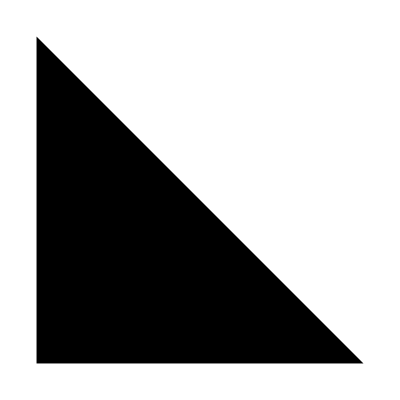

```mathematica
Graphics@Triangle[]
```

注意：本质上，前面的 Plot 和 Chart 都是 Graphics！它们的底层是统一的。这一点会在进阶课程里凸显出其重要意义。

同样有二维 Graphics 和三维 Graphics3D，他们是很相似的。让我们从二维说起：

Graphics 的基本语法

Graphics[primitives, options]

primitives 是一个列表，根据里面的「图形指令」按顺序绘制。「图形指令」包括样式和图形对象，前面的样式会影响所在括号内的所有对象。
options 选项则与前面绘图函数的类似。

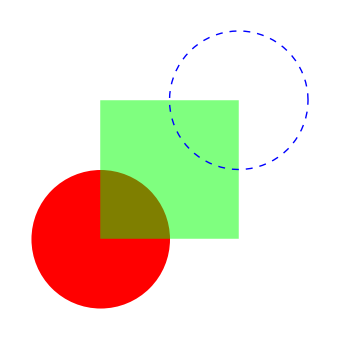

```mathematica
Graphics[{
Red,Disk[],
{Opacity[.5],Green,Rectangle[{0,0},{2,2}]},
Thick,Dashed,Blue,Circle[{2,2}]},
ImageSize->Medium
]
```

图形对象（图元）

Mathematica 内置了一大堆几何图形对象，包括 0-3 维（点、线、面、体）的各种常用对象（甚至包括高维，但没法画出来）。我们可以自由组合这些对象，来画出各种精巧或逼真的 Graphics。

帮助文档中的指南：
guide/GraphicsObjects
guide/GeometricSpecialRegions

顺便一提：这些对象也可以作为「几何区域」，用于各种计算，比如区域上的积分、求根、最优化、绘图等等。

## 图形对象函数举例

这些函数也都有着灵活的用法，可以详见它们的文档页面。这里以最常用的对象——二维圆盘举例：
（F1 打开帮助文档）

```mathematica
Disk
```

除了简单的圆，还可以表示椭圆、扇形、（椭扇形），还有多个同样的圆（高效表示）。

图形指令

图形指令包括各种你想到或没想到的定制，比如颜色、粗细、大小、透明度、线条样式、箭头样式，甚至纹理、阴影、光晕，对于 3D 对象甚至还有光照效果！

guide/GraphicsDirectives

Directive 复合指令

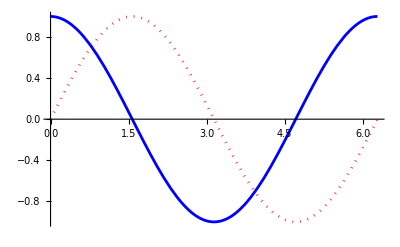

```mathematica
Plot[{Sin@x,Cos@x},{x,0,2π},PlotStyle->{Directive[Red,Dotted],Blue}]
```

例子：

## 画一棵松树

```mathematica
pinetree[p_,s_]:=s{{-1,-1,p/s},{1,-1,p/s},{1,1,p/s},{-1,1,p/s},{0,0,p/s+1}};

Graphics3D[{Brown,Cylinder[{{0,0,-1},{0,0,1}},1],Green,Table[Pyramid@pinetree[2i-1,6-i],{i,4}]}
]
```

-Graphics3D-

## 14.0 新功能：纹理贴图

非常酷的贴图！！！

```mathematica
Graphics3D[{Texture[Entity["PlanetaryMoon","Moon"]["CylindricalEquidistantTexture"]],Sphere[TextureMapping->"Spherical"]},Lighting->"Accent"]
```

-Graphics3D-

还可以用来当背景

```mathematica
env={Texture[-Graphics-],Black,Sphere[{0,0,0},100,TextureMapping->"Spherical"]};
Graphics3D[{env,Torus[]},ViewVector->{{-1,-2,1},{0,0,0}},Method->{"RotationControl"->"Globe"}]
```

-Graphics3D-

或者把二者结合——

```mathematica
Graphics3D[{{Texture[-Graphics-],Black,Sphere[{0,0,0},100,TextureMapping->"Spherical"]},Texture[Entity["Planet","Earth"]["CylindricalEquidistantTexture"]],Sphere[{0,0,0},TextureMapping->"Spherical"]},Method->{"RotationControl"->"Globe"},Lighting->"Accent",Boxed->False,ViewVector->{{-3,-1,0.75},{0,0,0}}]
```

-Graphics3D-

## 组合图形和绘图

前面的每一种绘图方法都已经很强大，但我们还可以把它们组合起来使用，以实现更复杂的绘图。

Show 函数：把不同的图形组合起来

Show 函数可以把多个 Graphics （当然也包括各种 Plot 和 Chart）组合在一起。还可以用来改变他们的绘图选项。

其他插入图形的方法

Inset 插图
Prolog, Epilog 选项，在绘图前/后绘制的图形

例子：把数据和拟合结果画在一起

```mathematica
data=Table[{x,Cos[2x]Exp[-x/5]+RandomReal[{-.1,.1}]},
{x,0.,10,.01}];
model=NonlinearModelFit[data,Cos[k x]Exp[-x/L],{k,L},x]
```

FittedModel[…]

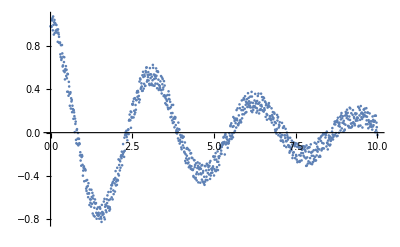

```mathematica
ListPlot[data]
```

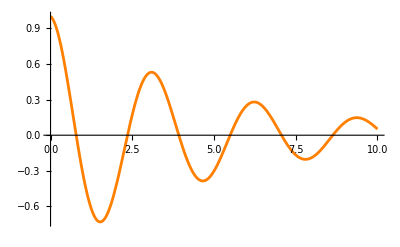

```mathematica
Plot[model@x,{x,0,10},PlotStyle->Orange]
```

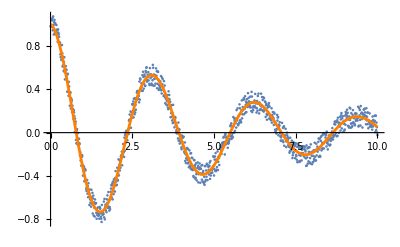

```mathematica
Show[ListPlot[data],
Plot[model@x,{x,0,10},PlotStyle->Orange]]
```

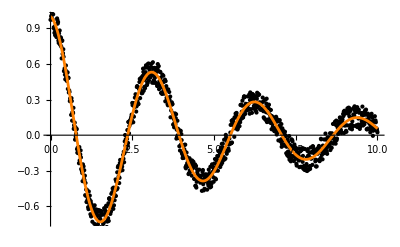

```mathematica
Plot[model@x,{x,0,10},PlotStyle->Orange,Prolog->{Point@data}]
```

## 绘图选项

参见帮助文档：
guide/GraphicsOptionsAndStyling
guide/PlottingOptions

坐标轴缩放

```mathematica
ScalingFunctions
```

支持许多常用的缩放，包括 对数、倒数、翻转、无穷尺度 等，还支持日期、分类等轴，可完全自定义。

另外，部分常用函数有对应的 Log 版本，比如：

```mathematica
LogLogPlot,         LogPlot,         LogLinearPlot,
ListLogLogPlot,ListLogPlot,ListLogLinearPlot
```

绘图标注

PlotLegend 图例

PlotLabels 标签

PlotLabel 标题

AxesLabel 坐标轴标签

绘图范围

PlotRange

RegionFunction

控制绘图精度

PlotPoints （初始）绘图点数

MaxRecursion 递归细化次数

绘图比例和大小

ImageSize 图像大小

AspectRatio 宽高比（2D）

BoxRatios 边界框比例 （3D）

绘图样式

PlotStyle 绘图样式

ColorFunction 颜色函数

PlotTheme 预定义的主题

坐标轴和边框

Axes 系列：

AxesLabel

Ticks

AxesOrigin

Frame 系列：

FrameLabel

FrameTicks

三维图形选项

guide/3DGraphicsOptions

网格选项

```mathematica
Mesh,MeshFunctions,MeshStyle,MeshShading
```

## 与图形交互

guide/DynamicVisualization

二维图形交互

```mathematica
Tooltip
```

```mathematica
PlotHighlighting
```

三维图形交互

guide/Interactive3DControl
tutorial/InteractiveGraphics3DInteraction

旋转、垂直于屏幕旋转

放大缩小

平移

右键菜单：正面图、顶视图、缺省图、重置移动/放大

## 动态交互简介

```mathematica
Manipulate
```

例子：

两个点电荷的电势

```mathematica
Manipulate[
ContourPlot[q1/Norm[{x,y}-p[[1]]]+q2/Norm[{x,y}-p[[2]]],{x,-2,2},{y,-2,2},Contours->10,ImageSize->Large,PlotLegends->Automatic,PerformanceGoal->"Quality"]
,{{q1,-1},-3,3},{{q2,1},-3,3},{{p,{{-1,0},{1,0}}},{-1,-1},{1,1},Locator},Deployed->True,SaveDefinitions->True]
```

PT 题目「飓风球」的欧拉角演示

```mathematica
hurriballs[θ_, ϕ_, ψ_, R_ : 1] := {Ball[R {Sin[θ] Cos[ϕ], Sin[θ] Sin[ϕ], Cos[θ]}, R], Ball[-R {Sin[θ] Cos[ϕ], Sin[θ] Sin[ϕ], Cos[θ]}, R]};
arrows[θ_, ϕ_, ψ_, R_ : 1] := {Arrow[{-3 R {Sin[θ] Cos[ϕ], Sin[θ] Sin[ϕ], Cos[θ]}, 3 R {Sin[θ] Cos[ϕ], Sin[θ] Sin[ϕ], Cos[θ]}}], Arrow[{{0, 0, 0}, 1.5 R FullSimplify[RotationTransform[ϕ, {0, 0, 1}]@RotationTransform[ψ, {Sin[θ], 0, Cos[θ]}]@RotationTransform[θ, {0, 1, 0}]@{-1, 0, 0}, {θ, ψ, ϕ} ∈ Reals]}]};
```

```mathematica
Manipulate[
Graphics3D[
Evaluate@{
Style[hurriballs[θ,ϕ,ψ],{MaterialShading["Iron"],Lighting->"ThreePoint"}],arrows[θ,ϕ,ψ],InfinitePlane[{{0,0,0},{0,1,0},{1,0,0}}-1-Cos[θ]]},
PlotRange->{{-3,3},{-3,3},{-4-Cos[θ],4-Cos[θ]}},ImageSize->600],
{θ,0,π/2},{ϕ,0,2π},{ψ,0,2π},SaveDefinitions->True]
```

可视化显示线性微分方程 x'==A.x 的解：

```mathematica
A=({{-1.1, 0.9}, {-1.4, 0.3}});
```

```mathematica
Manipulate[ParametricPlot[Evaluate[MatrixExp[A t,#]&/@pt],{t,0,10},PlotRange->5],{{pt,{{2,0},{0,1},{-3,0}}},Locator},SaveDefinitions->True]
```

可视化薛定谔方程的解：波包的演化

```mathematica
ListAnimate[Table[DensityPlot[Abs[solution[t,x,y]],{x,y}∈ Ω,],{t,0,8,0.1} ],]
```

## 其他

```mathematica
s=StreamPlot[Evaluate@Grad[Sin[x+y^2],{x,y}],{x,-3,3},{y,-2,2},Frame->False,PlotRangePadding->None];
c=ContourPlot[Sin[x+y^2],{x,-3,3},{y,-2,2},Frame->False,PlotRangePadding->None];
Plot3D[{Sin[x+y^2],-3},{x,-3,3},{y,-2,2},PlotStyle->{Texture[s],Texture[c]},Mesh->None]
```

-Graphics3D-

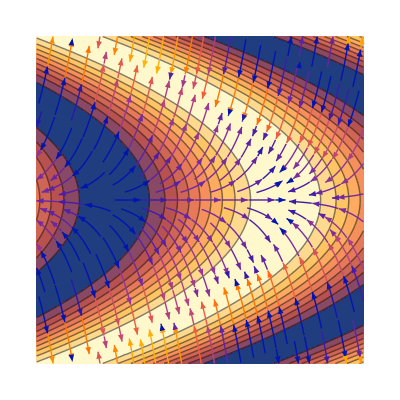

```mathematica
Show[c,s]
```

初始化单元

新手注意：
在本文档中，按「单元组」指定 Context，因此一个单元组之外的符号定义是不共享的，与其他笔记本之间也不共享。
这样的 Behavior 与 MMA 文档类似，而和通常的笔记本不同。通常自己写的笔记本，都是全局变量。

```mathematica
SetOptions[EvaluationNotebook[],CellContext->CellGroup]
```